## Definitions

```mathematica
f[x_]:=UnitStep[x-1];
L = N@2π;
```

```mathematica
An[n_]:=Sqrt[(1/L)]NIntegrate[f[x]*Exp[-2ⅈ*n*π*x/L],{x,0,L}];
```

```mathematica
fapprox[x_,$N_]:=Sqrt[1/L]Sum[An[n]Exp[2ⅈ*n*π*x/L],{n,-$N,$N}];
```

```mathematica
out = fapprox[x,50]
```

0.398942 (2.10769-(0.335698+0.183393 ⅈ) ⅇ^((0.-1. ⅈ) x)-(0.335698-0.183393 ⅈ) ⅇ^((0.+1. ⅈ) x)-(0.181379+0.28248 ⅈ) ⅇ^((0.-2. ⅈ) x)-(0.181379-0.28248 ⅈ) ⅇ^((0.+2. ⅈ) x)-(0.0187662+0.264631 ⅈ) ⅇ^((0.-3. ⅈ) x)-(0.0187662-0.264631 ⅈ) ⅇ^((0.+3. ⅈ) x)+(0.0754801-0.164927 ⅈ) ⅇ^((0.-4. ⅈ) x)+(0.0754801+0.164927 ⅈ) ⅇ^((0.+4. ⅈ) x)+(0.0765111-0.0571555 ⅈ) ⅇ^((0.-5. ⅈ) x)+(0.0765111+0.0571555 ⅈ) ⅇ^((0.+5. ⅈ) x)+(0.0185784-0.00264829 ⅈ) ⅇ^((0.-6. ⅈ) x)+(0.0185784+0.00264829 ⅈ) ⅇ^((0.+6. ⅈ) x)-(0.0374428+0.0140255 ⅈ) ⅇ^((0.-7. ⅈ) x)-(0.0374428-0.0140255 ⅈ) ⅇ^((0.+7. ⅈ) x)-(0.0493371+0.0571235 ⅈ) ⅇ^((0.-8. ⅈ) x)-(0.0493371-0.0571235 ⅈ) ⅇ^((0.+8. ⅈ) x)-(0.0182679+0.0847145 ⅈ) ⅇ^((0.-9. ⅈ) x)-(0.0182679-0.0847145 ⅈ) ⅇ^((0.+9. ⅈ) x)+(0.0217033-0.0733683 ⅈ) ⅇ^((0.-10. ⅈ) x)+(0.0217033+0.0733683 ⅈ) ⅇ^((0.+10. ⅈ) x)+(0.0362671-0.036107 ⅈ) ⅇ^((0.-11. ⅈ) x)+(0.0362671+0.036107 ⅈ) ⅇ^((0.+11. ⅈ) x)+(0.0178385-0.0051911 ⅈ) ⅇ^((0.-12. ⅈ) x)+(0.0178385+0.0051911 ⅈ) ⅇ^((0.+12. ⅈ) x)-(0.012894+0.00284026 ⅈ) ⅇ^((0.-13. ⅈ) x)-(0.012894-0.00284026 ⅈ) ⅇ^((0.+13. ⅈ) x)-(0.0282282+0.0245994 ⅈ) ⅇ^((0.-14. ⅈ) x)-(0.0282282-0.0245994 ⅈ) ⅇ^((0.+14. ⅈ) x)-(0.0172952+0.0468009 ⅈ) ⅇ^((0.-15. ⅈ) x)-(0.0172952-0.0468009 ⅈ) ⅇ^((0.+15. ⅈ) x)+(0.00717855-0.0488121 ⅈ) ⅇ^((0.-16. ⅈ) x)+(0.00717855+0.0488121 ⅈ) ⅇ^((0.+16. ⅈ) x)+(0.0225613-0.0299245 ⅈ) ⅇ^((0.-17. ⅈ) x)+(0.0225613+0.0299245 ⅈ) ⅇ^((0.+17. ⅈ) x)+(0.0166445-0.00752856 ⅈ) ⅇ^((0.-18. ⅈ) x)+(0.0166445+0.00752856 ⅈ) ⅇ^((0.+18. ⅈ) x)-(0.00314697+0.000237169 ⅈ) ⅇ^((0.-19. ⅈ) x)-(0.00314697-0.000237169 ⅈ) ⅇ^((0.+19. ⅈ) x)-(0.0182106+0.0118071 ⅈ) ⅇ^((0.-20. ⅈ) x)-(0.0182106-0.0118071 ⅈ) ⅇ^((0.+20. ⅈ) x)-(0.0158942+0.0294026 ⅈ) ⅇ^((0.-21. ⅈ) x)-(0.0158942-0.0294026 ⅈ) ⅇ^((0.+21. ⅈ) x)+(0.000160507-0.0362668 ⅈ) ⅇ^((0.-22. ⅈ) x)+(0.000160507+0.0362668 ⅈ) ⅇ^((0.+22. ⅈ) x)+(0.014678-0.0265875 ⅈ) ⅇ^((0.-23. ⅈ) x)+(0.014678+0.0265875 ⅈ) ⅇ^((0.+23. ⅈ) x)+(0.0150531-0.00957164 ⅈ) ⅇ^((0.-24. ⅈ) x)+(0.0150531+0.00957164 ⅈ) ⅇ^((0.+24. ⅈ) x)+(0.00211203-0.000140383 ⅈ) ⅇ^((0.-25. ⅈ) x)+(0.00211203+0.000140383 ⅈ) ⅇ^((0.+25. ⅈ) x)-(0.0117006+0.00541765 ⅈ) ⅇ^((0.-26. ⅈ) x)-(0.0117006-0.00541765 ⅈ) ⅇ^((0.+26. ⅈ) x)-(0.0141311+0.0190922 ⅈ) ⅇ^((0.-27. ⅈ) x)-(0.0141311-0.0190922 ⅈ) ⅇ^((0.+27. ⅈ) x)-(0.00385985+0.0279631 ⅈ) ⅇ^((0.-28. ⅈ) x)-(0.00385985-0.0279631 ⅈ) ⅇ^((0.+28. ⅈ) x)+(0.00912937-0.0240474 ⅈ) ⅇ^((0.-29. ⅈ) x)+(0.00912937+0.0240474 ⅈ) ⅇ^((0.+29. ⅈ) x)+(0.0131389-0.0112468 ⅈ) ⅇ^((0.-30. ⅈ) x)+(0.0131389+0.0112468 ⅈ) ⅇ^((0.+30. ⅈ) x)+(0.0051996-0.00109719 ⅈ) ⅇ^((0.-31. ⅈ) x)+(0.0051996+0.00109719 ⅈ) ⅇ^((0.+31. ⅈ) x)-(0.00687461+0.00206673 ⅈ) ⅇ^((0.-32. ⅈ) x)-(0.00687461-0.00206673 ⅈ) ⅇ^((0.+32. ⅈ) x)-(0.0120881+0.0122497 ⅈ) ⅇ^((0.-33. ⅈ) x)-(0.0120881-0.0122497 ⅈ) ⅇ^((0.+33. ⅈ) x)-(0.00620804+0.0216904 ⅈ) ⅇ^((0.-34. ⅈ) x)-(0.00620804-0.0216904 ⅈ) ⅇ^((0.+34. ⅈ) x)+(0.00488058-0.021699 ⅈ) ⅇ^((0.-35. ⅈ) x)+(0.00488058+0.021699 ⅈ) ⅇ^((0.+35. ⅈ) x)+(0.0109906-0.0124998 ⅈ) ⅇ^((0.-36. ⅈ) x)+(0.0109906+0.0124998 ⅈ) ⅇ^((0.+36. ⅈ) x)+(0.00693877-0.00252936 ⅈ) ⅇ^((0.-37. ⅈ) x)+(0.00693877+0.00252936 ⅈ) ⅇ^((0.+37. ⅈ) x)-(0.00311142+0.000471658 ⅈ) ⅇ^((0.-38. ⅈ) x)-(0.00311142-0.000471658 ⅈ) ⅇ^((0.+38. ⅈ) x)-(0.00985894+0.00750172 ⅈ) ⅇ^((0.-39. ⅈ) x)-(0.00985894-0.00750172 ⅈ) ⅇ^((0.+39. ⅈ) x)-(0.00743143+0.0166253 ⅈ) ⅇ^((0.-40. ⅈ) x)-(0.00743143-0.0166253 ⅈ) ⅇ^((0.+40. ⅈ) x)+(0.00154345-0.0193374 ⅈ) ⅇ^((0.-41. ⅈ) x)+(0.00154345+0.0193374 ⅈ) ⅇ^((0.+41. ⅈ) x)+(0.0087057-0.0132979 ⅈ) ⅇ^((0.-42. ⅈ) x)+(0.0087057+0.0132979 ⅈ) ⅇ^((0.+42. ⅈ) x)+(0.00771698-0.00412754 ⅈ) ⅇ^((0.-43. ⅈ) x)+(0.00771698+0.00412754 ⅈ) ⅇ^((0.+43. ⅈ) x)-(0.000160501+1.4207×10^-6 ⅈ) ⅇ^((0.-44. ⅈ) x)-(0.000160501-1.4207×10^-6 ⅈ) ⅇ^((0.+44. ⅈ) x)-(0.00754359+0.0042082 ⅈ) ⅇ^((0.-45. ⅈ) x)-(0.00754359-0.0042082 ⅈ) ⅇ^((0.+45. ⅈ) x)-(0.0078209+0.0124208 ⅈ) ⅇ^((0.-46. ⅈ) x)-(0.0078209-0.0124208 ⅈ) ⅇ^((0.+46. ⅈ) x)-(0.00104891+0.0169112 ⅈ) ⅇ^((0.-47. ⅈ) x)-(0.00104891-0.0169112 ⅈ) ⅇ^((0.+47. ⅈ) x)+(0.00638519-0.0136317 ⅈ) ⅇ^((0.-48. ⅈ) x)+(0.00638519+0.0136317 ⅈ) ⅇ^((0.+48. ⅈ) x)+(0.00776515-0.00569435 ⅈ) ⅇ^((0.-49. ⅈ) x)+(0.00776515+0.00569435 ⅈ) ⅇ^((0.+49. ⅈ) x)+(0.00209345-0.000279531 ⅈ) ⅇ^((0.-50. ⅈ) x)+(0.00209345+0.000279531 ⅈ) ⅇ^((0.+50. ⅈ) x))

```mathematica
Abs@An[1]
```

0.305212

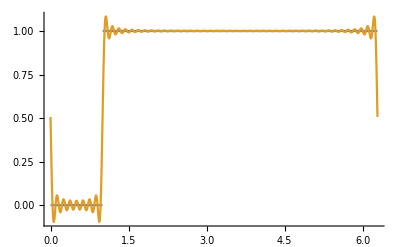

```mathematica
Plot[{f[x],Re@out},{x,0,L},PlotRange->All]
```

```mathematica
Re@FourierTransform[Sin[x],x,ω]
```

-√(π/2) Im[DiracDelta[-1+ω]]+√(π/2) Im[DiracDelta[1+ω]]

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in x in the region {{-∞,∞}}. NIntegrate obtained 0.+4.52066×10^307 ⅈ and 6.79366×10^307 for the integral and error estimates.

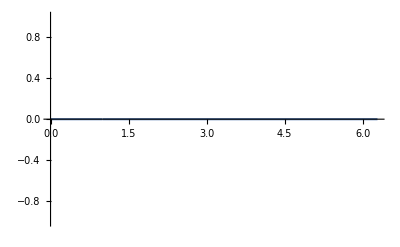

```mathematica
Show[{Plot[Re@FourierTransform[Sin[x],x,ω],{ω,0,2Pi}]}]
```